```mathematica
$Assumptions=And[M>2,df>0,q>0,df<1/2,q<1,M/2∈ℕ,β>0,β<1];
```

```mathematica
f[β_,M_]=(1-β^(M-1))/(1-β^M)-(M-1)/M;
```

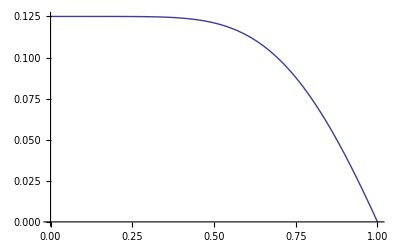

```mathematica
Plot[f[β,8],{β,0,1}]
```

```mathematica
D[f[β,M],β]//Simplify
```

-(β^(-2+M) (-1+M-M β+β^M))/((-1+β^M)^2)

```mathematica
g[df_,β_,M_]=2((1-2df)^(M-1)-β^(M-1)(1+2df)^(M-1))/((1-2df)^M-β^M(1+2df)^M);
```

```mathematica
D[g[df,β,M],df]//Simplify
```

(2 (-M (-2 (1-2 df)^(-1+M)-2 (1+2 df)^(-1+M) β^M) ((1-2 df)^(-1+M)-(β+2 df β)^(-1+M))+2 (-1+M) (-(1-2 df)^(-2+M)-(1+2 df)^(-2+M) β^(-1+M)) ((1-2 df)^M-(β+2 df β)^M)))/((1-2 df)^M-(β+2 df β)^M)^2

```mathematica
D[g[df,β,M],{df,2}]//FullSimplify
```

(2 (-4 (-1+M) M (-(1-2 df)^(-2+M)-(1+2 df)^(-2+M) β^(-1+M)) (-2 (1-2 df)^(-1+M)-2 (1+2 df)^(-1+M) β^M) ((1-2 df)^M-(β+2 df β)^M)+4 (-2+M) (-1+M) ((1-2 df)^(-3+M)-(1+2 df)^(-3+M) β^(-1+M)) ((1-2 df)^M-(β+2 df β)^M)^2+((1-2 df)^(-1+M)-(β+2 df β)^(-1+M)) (8 M^2 ((1-2 df)^(-1+M)+(1+2 df)^(-1+M) β^M)^2-4 (-1+M) M ((1-2 df)^(-2+M)-(1+2 df)^(-2+M) β^M) ((1-2 df)^M-(β+2 df β)^M))))/((1-2 df)^M-(β+2 df β)^M)^3

```mathematica
Limit[g[df,β,M],df->0]//Simplify
```

(2 (-β+β^M))/(β (-1+β^M))

```mathematica
gmin=Limit[g[df,β,M],df->1/2]//Simplify
```

1/β

```mathematica
testdf[β_,M_]=gmin-g[0,β,M]/2
```

1/β-(1-β^(-1+M))/(1-β^M)

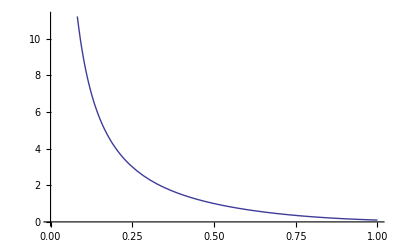

```mathematica
Plot[testdf[β,10],{β,0,1}]
```

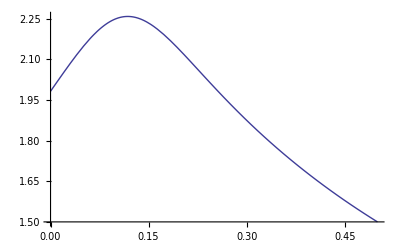

```mathematica
Plot[g[df,2/3,10],{df,0,0.5},PlotRange->Full]
```

```mathematica
dfp[β_,M_]:=Plot[g[df,β,M]-g[0,β,M]/2,{df,0,0.5},PlotRange->Full]
```

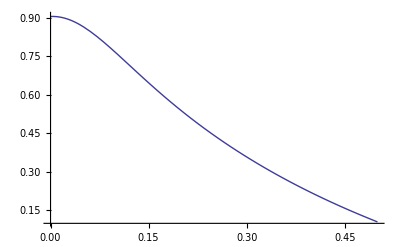

```mathematica
dfp[0.99,10]
```